```mathematica
plot[f_]:=Plot[{f,2/γ}/.γ->{1,1.2,2,5,10,100},{θ,0,π},PlotStyle->{Thickness[0.0035]},Frame->{{True,True},{True,True}},FrameTicks->{{{0,π/4,π/2,3 π/4,π},Automatic},{{0,π/4,π/2,3 π/4,π},Automatic}},
PlotRange->{{0,π},{0,π}}
]
```

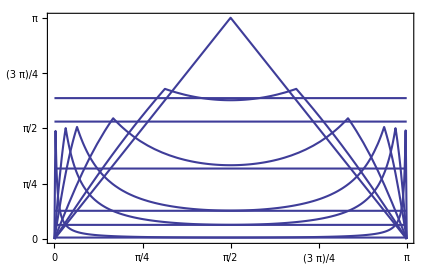

```mathematica
plot[
ArcSin[Sin[θ]/(γ+√(γ^2-1) Cos[θ])]+ArcSin[Sin[θ]/(γ-√(γ^2-1) Cos[θ])]
]
```

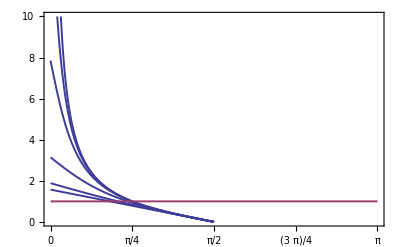

```mathematica
plot[
γ/2(ArcTan[Sin[θ],γ Cos[θ]+√(γ^2-1)]+ArcTan[Sin[θ],γ Cos[θ]-√(γ^2-1)])
]
```

```mathematica
TrigExpand[(γ+{1,-1}√(γ^2-1) Cos[θ])^2-(Sin[θ])^2]
```

{-1+(3 γ^2)/2+2 γ √(-1+γ^2) Cos[θ]+1/2 γ^2 Cos[θ]^2-1/2 γ^2 Sin[θ]^2,-1+(3 γ^2)/2-2 γ √(-1+γ^2) Cos[θ]+1/2 γ^2 Cos[θ]^2-1/2 γ^2 Sin[θ]^2}

```mathematica
TrigReduce[1/2 γ^2 Cos[θ]^2-1/2 γ^2 Sin[θ]^2]
```

1/2 γ^2 Cos[2 θ]

```mathematica
TrigReduce[γ^2 Cos[θ]^2-1/2 γ^2]
```

1/2 γ^2 Cos[2 θ]

```mathematica
Expand[-1+(3 γ^2)/2+2 γ √(-1+γ^2) x+γ^2 x^2-1/2 γ^2]
```

-1+γ^2+x^2 γ^2+2 x γ √(-1+γ^2)

```mathematica
Simplify[y^2+x^2 γ^2+2 x γ y]
```

(y+x γ)^2

```mathematica
√(-1+γ^2)+x γ
```

```mathematica
TrigReduce[(γ+{1,-1}√(γ^2-1) Cos[θ])^2-(Sin[θ])^2]
```

{1/2 (-2+3 γ^2+4 γ √(-1+γ^2) Cos[θ]+γ^2 Cos[2 θ]),1/2 (-2+3 γ^2-4 γ √(-1+γ^2) Cos[θ]+γ^2 Cos[2 θ])}

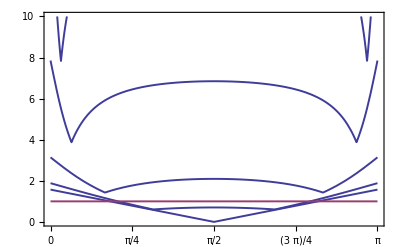

```mathematica
plot[γ/2(ArcTan[Sin[θ],√(1/2 (-2+3 γ^2+4 γ √(-1+γ^2) Cos[θ]+γ^2 Cos[2 θ]))]+ArcTan[Sin[θ],√(1/2 (-2+3 γ^2-4 γ √(-1+γ^2) Cos[θ]+γ^2 Cos[2 θ]))])
]
```